## Sierpinski’s Carpet Solution

Hello and welcome to the solution to the Sierpinski’s Carpet project. Please try to solve the project yourself before looking at the answer. Practice makes perfect!

### Introduction

In this lecture, we will demonstrate how to produce a Manipulate of Sierpinski’s Carpet:

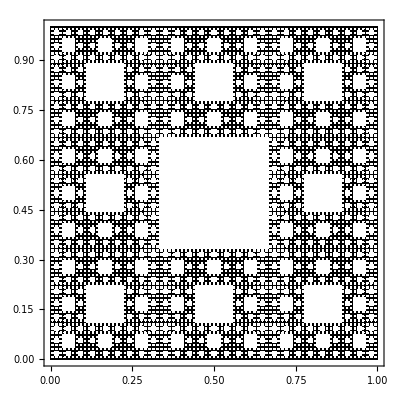

### Construction

To construct Sierpinski’s Carpet, start with a black square.

Divide the black square into a grid of equal sized 3x3 sub-squares.

Make the middle square white.

Repeat steps 2 and 3 recursively on the remaining 8 black sub-squares.

### Solution

#### Step 1: Start with a black square.

Let’s get started by drawing the initial black square, which is our initial condition:

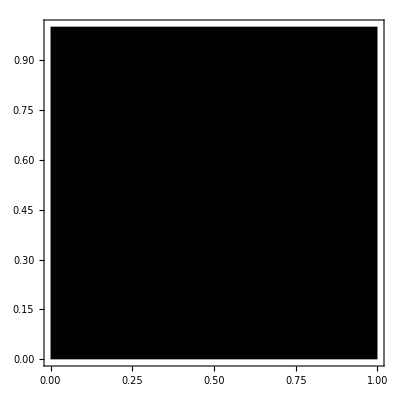

```mathematica
Graphics[{
{Black,Rectangle[{0,0},{1,1}]}
},Frame->True]
```

#### Step 2: Divide the black square(s) into 9 sub-squares

Now, we need to divide the rectangle into 9 mini squares, where each mini square is also black, except for the center one, which will be white. Let’s use a replacement rule. If we see a black square, we’ll want to divide it up into 9 pieces.

So let’s make a rule that matches black squares, and when it matches, we’ll replace it with 9 sub-squares:

```mathematica
{Black,Rectangle[{0,0},{1,1}]}/.
{Black,Rectangle[{x1_,y1_},{x2_,y2_}]}:>
Table[
{i,j},
{i,0,2},{j,0,2}]
```

{{{0,0},{0,1},{0,2}},{{1,0},{1,1},{1,2}},{{2,0},{2,1},{2,2}}}

#### Step 3: Make the middle square white

Now let’s add the black and white colors to the sub-squares. All the squares are black, except for the one at position 1,1, which will be white:

```mathematica
{Black,Rectangle[{0,0},{1,1}]}/.
{Black,Rectangle[{x1_,y1_},{x2_,y2_}]}:>
Table[
{If[i==1&&j==1,White,Black],i,j},
{i,0,2},{j,0,2}]
```

{{{GrayLevel[0],0,0},{GrayLevel[0],0,1},{GrayLevel[0],0,2}},{{GrayLevel[0],1,0},{GrayLevel[1],1,1},{GrayLevel[0],1,2}},{{GrayLevel[0],2,0},{GrayLevel[0],2,1},{GrayLevel[0],2,2}}}

Now, for each i and j, we need to create a square that is 1/3 the size of the original. 1/3 the size of the original is given by (x2-x1)/3. Let’s use a With function to hold the size, since we will use it several times later on:

```mathematica
{Black,Rectangle[{0,0},{1,1}]}/.
{Black,Rectangle[{x1_,y1_},{x2_,y2_}]}:>
With[{s=(x2-x1)/3},
Table[
{If[i==1&&j==1,White,Black],i,j},
{i,0,2},{j,0,2}]
]
```

{{{GrayLevel[0],0,0},{GrayLevel[0],0,1},{GrayLevel[0],0,2}},{{GrayLevel[0],1,0},{GrayLevel[1],1,1},{GrayLevel[0],1,2}},{{GrayLevel[0],2,0},{GrayLevel[0],2,1},{GrayLevel[0],2,2}}}

The i’th and j’th position will be (x1+i)×s and (y1+j)×s:

```mathematica
{Black,Rectangle[{0,0},{1,1}]}/.
{Black,Rectangle[{x1_,y1_},{x2_,y2_}]}:>
With[{s=(x2-x1)/3},
Table[
{If[i==1&&j==1,White,Black],x1+i s,y1+j s},
{i,0,2},{j,0,2}]
]
```

{{{GrayLevel[0],0,0},{GrayLevel[0],0,1/3},{GrayLevel[0],0,2/3}},{{GrayLevel[0],1/3,0},{GrayLevel[1],1/3,1/3},{GrayLevel[0],1/3,2/3}},{{GrayLevel[0],2/3,0},{GrayLevel[0],2/3,1/3},{GrayLevel[0],2/3,2/3}}}

So that’s the top left point of the square. Let’s wrap it in a list and add the bottom right point, which is the same as the first point, except we add 1 to i and j:

```mathematica
{Black,Rectangle[{0,0},{1,1}]}/.
{Black,Rectangle[{x1_,y1_},{x2_,y2_}]}:>
With[{s=(x2-x1)/3},
Table[
{If[i==1&&j==1,White,Black],{x1+i s,y1+j s},{x1+(i+1) s,y1+(j+1) s}},
{i,0,2},{j,0,2}]
]
```

{{{GrayLevel[0],{0,0},{1/3,1/3}},{GrayLevel[0],{0,1/3},{1/3,2/3}},{GrayLevel[0],{0,2/3},{1/3,1}}},{{GrayLevel[0],{1/3,0},{2/3,1/3}},{GrayLevel[1],{1/3,1/3},{2/3,2/3}},{GrayLevel[0],{1/3,2/3},{2/3,1}}},{{GrayLevel[0],{2/3,0},{1,1/3}},{GrayLevel[0],{2/3,1/3},{1,2/3}},{GrayLevel[0],{2/3,2/3},{1,1}}}}

Great! Now we just put the two points into a Rectangle to make them renderable by the Graphics function:

```mathematica
{Black,Rectangle[{0,0},{1,1}]}/.
{Black,Rectangle[{x1_,y1_},{x2_,y2_}]}:>
With[{s=(x2-x1)/3},
Table[
{If[i==1&&j==1,White,Black],Rectangle[{x1+i s,y1+j s},{x1+(i+1) s,y1+(j+1) s}]},
{i,0,2},{j,0,2}]
]
```

{{{GrayLevel[0],Rectangle[{0,0},{1/3,1/3}]},{GrayLevel[0],Rectangle[{0,1/3},{1/3,2/3}]},{GrayLevel[0],Rectangle[{0,2/3},{1/3,1}]}},{{GrayLevel[0],Rectangle[{1/3,0},{2/3,1/3}]},{GrayLevel[1],Rectangle[{1/3,1/3},{2/3,2/3}]},{GrayLevel[0],Rectangle[{1/3,2/3},{2/3,1}]}},{{GrayLevel[0],Rectangle[{2/3,0},{1,1/3}]},{GrayLevel[0],Rectangle[{2/3,1/3},{1,2/3}]},{GrayLevel[0],Rectangle[{2/3,2/3},{1,1}]}}}

Cool! Let’s render it:

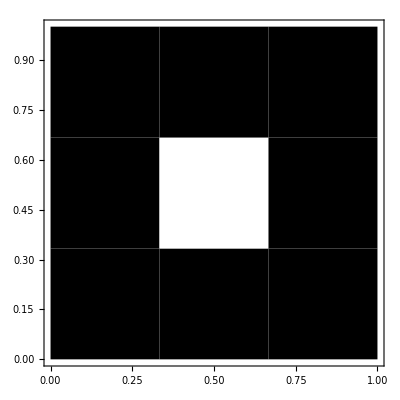

```mathematica
Graphics[
{Black,Rectangle[{0,0},{1,1}]}/.
{Black,Rectangle[{x1_,y1_},{x2_,y2_}]}:>
With[{s=(x2-x1)/3},
Table[
{If[i==1&&j==1,White,Black],Rectangle[{x1+i s,y1+j s},{x1+(i+1) s,y1+(j+1) s}]},
{i,0,2},{j,0,2}]
],
Frame->True
]
```

Beautiful!

#### Step 4: Recursively apply steps 2 and 3

The replacement rule we used has gotten quite big. Let’s save it to a variable so that it’s easier to work with:

```mathematica
divideRule={Black,Rectangle[{x1_,y1_},{x2_,y2_}]}:>
With[{s=(x2-x1)/3},
Table[
{If[i==1&&j==1,White,Black],Rectangle[{x1+i s,y1+j s},{x1+(i+1) s,y1+(j+1) s}]},
{i,0,2},{j,0,2}]
];
```

Let’s test it out again:

```mathematica
Graphics[{
{Black,Rectangle[{0,0},{1,1}]}/.divideRule
},Frame->True]
```

-Graphics-

Let’s apply the rule twice by using Nest:

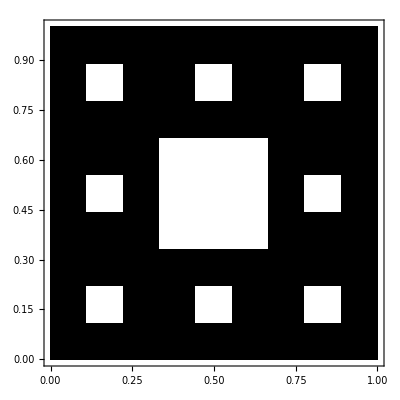

```mathematica
Graphics[{
Nest[#/.divideRule&,{Black,Rectangle[{0,0},{1,1}]},2]
},Frame->True]
```

Now, let’s wrap it in a Manipulate:

```mathematica
Manipulate[
Graphics[
Nest[#/.divideRule&,{Black,Rectangle[{0,0},{1,1}]},i],
Frame->True
],{i,0,5,1}
]
```

Awesome!

### Optimization

Notice how slow it is when going from 3 to 4 iterations, and especially from 4 to 5? Part of the reason why it’s so slow is that we have so many squares to draw. But notice that when we’re rendering, we can start by drawing a single black square as a sort of canvas, and then we only really need to draw the white squares. Let’s optimize our code to just draw white squares.

So we start by drawing the black square:

```mathematica
Manipulate[
Graphics[{
Black,Rectangle[{0,0},{1,1}],
Nest[#/.divideRule&,{Black,Rectangle[{0,0},{1,1}]},i]
},Frame->True
],{i,0,5,1}
]
```

Now we need to pull out all of the white squares from the result:

```mathematica
Cases[Nest[#/.divideRule&,{Black,Rectangle[{0,0},{1,1}]},2],{White,_},All]
```

{{GrayLevel[1],Rectangle[{1/9,1/9},{2/9,2/9}]},{GrayLevel[1],Rectangle[{1/9,4/9},{2/9,5/9}]},{GrayLevel[1],Rectangle[{1/9,7/9},{2/9,8/9}]},{GrayLevel[1],Rectangle[{4/9,1/9},{5/9,2/9}]},{GrayLevel[1],Rectangle[{1/3,1/3},{2/3,2/3}]},{GrayLevel[1],Rectangle[{4/9,7/9},{5/9,8/9}]},{GrayLevel[1],Rectangle[{7/9,1/9},{8/9,2/9}]},{GrayLevel[1],Rectangle[{7/9,4/9},{8/9,5/9}]},{GrayLevel[1],Rectangle[{7/9,7/9},{8/9,8/9}]}}

Let’s add that back to our Manipulate:

```mathematica
Manipulate[
Graphics[{
Black,Rectangle[{0,0},{1,1}],
Cases[Nest[#/.divideRule&,{Black,Rectangle[{0,0},{1,1}]},i],{White,_},All]
},Frame->True
],{i,0,5,1}
]
```

Still a little bit slow, but quite a lot faster than before!

### Summary

We hope you had fun making Sierpinski’s Carpet! We’ll see you at the next lecture.